```mathematica
Degree of Polarization;
```

```mathematica
Definitions;
```

```mathematica
P [Ioff_,Iab_,Ia_,Ib_]:= Sqrt[(Ioff-Ia)*(Ioff-Ib)/(Ioff*Iab-Ib*Ia)]
ΔP [Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_]:=Sqrt[(((Ib (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2-(-Ib+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2ΔIa^2+(((Ia (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2-(-Ia+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2ΔIb^2+((-(Iab (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2+(-Ia+Ioff)/(-Ia Ib+Iab Ioff)+(-Ib+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2 ΔIoff^2+(-(Ioff (-Ia+Ioff) (-Ib+Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)) (-Ia Ib+Iab Ioff)^2))^2ΔIab^2]
e1 [Ioff_,Iab_,Ia_,Ib_] :=(Iab-Ib)/(Ioff-Ia)
Δe1[Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_] := Sqrt[(((Iab-Ib)/(-Ia+Ioff)^2)*ΔIa)^2 +((-1/(-Ia+Ioff))*ΔIb)^2 +((-(Iab-Ib)/(-Ia+Ioff)^2)*ΔIoff)^2 +((1/(-Ia+Ioff))*ΔIab)^2 ]
e2 [Ioff_,Iab_,Ia_,Ib_] :=(Iab-Ia)/(Ioff-Ib)
Δe2 [Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_]:= Sqrt[((-1/(-Ib+Ioff))*ΔIa)^2 +(((-Ia+Iab)/(-Ib+Ioff)^2)*ΔIb)^2 +((-(-Ia+Iab)/(-Ib+Ioff)^2)*ΔIoff)^2 +((1/(-Ib+Ioff))*ΔIab)^2 ]
Flipp[CountsOff_,CountsOn_]:=CountsOff/CountsOn
ErrFlipp[CountsOff_,CountsOn_,ΔCountsOff_,ΔCountsOn_]:= Sqrt[((-CountsOff/CountsOn^2)*ΔCountsOn)^2 + ((1/CountsOn)*ΔCountsOff)^2 ]
Contrast[Imax_,Imin_]:=(Imax-Imin)/(Imax+Imin)
ErrContrast[Imax_,Imin_,ΔImax_,ΔImin_]:=Sqrt[(((2*Imin)/(Imax+Imin)^2)*ΔImax)^2+(((-2*Imax)/(Imax+Imin)^2)*ΔImin)^2]
k1[e_]:=1/2(e+1)
k2[e_]:=1/2(e+1)
Δk1[Δe_]:=1/2Δe
Δk2[Δe_]:=1/2Δe
```

```mathematica
File input;
```

## File Import

```mathematica
File1=Import["C:\\Users\\Kazu\\ownCloud\\! Exp Data\\3 Output POVM Uncertainty\\Experiment\\Raw Data\\measurements 23.11.2018\\2018-11-23-1325-degree-of-polarisation.dat"];
File2={{1220000,1220000,1220000,1220000,1283000,1283000,1283000,1283000,1346700,1346700,1346700,1346700,1410000,1410000,1410000,1410000,1437000,1437000,1437000,1437000,1463300,1463300,1463300,1463300,1490000,1490000,1490000,1490000,1507000,1507000,1507000,1507000,1523000,1523000,1523000,1523000,1540000,1540000,1540000,1540000,1573000,1573000,1573000,1573000,1607000,1607000,1607000,1607000,1640000,1640000,1640000,1640000,1670000,1670000,1670000,1670000,1707000,1707000,1707000,1707000,1740000,1740000,1740000,1740000,1757000,1757000,1757000,1757000,1773000,1773000,1773000,1773000,1790000,179000,1790000,1790000,1817000,1817000,1817000,1817000,1843000,1843000,1843000,1843000,1870000,1870000,1870000,1870000,1930000,1930000,1930000,1930000,1997000,1997000,1997000,1997000,2060000,2060000,2060000,2060000}};
position={1220000,1283000,1346700,1410000,1437000,1463300,1490000,1507000,1523000,1540000,1573000,1607000,1640000,1670000,1707000,1740000,1757000,1773000,1790000,1817000,1843000,1870000,1930000,1997000,2060000};
```

```mathematica
Caliculation;
Arrange;

Data1=File1[[5;;-1]];
Data2=Data1[[All,2]];
Intensities=Partition[Data2,4];

Ioff=Intensities[[All,1]];
Iab =Intensities[[All,4]];
Ia =Intensities[[All,2]];
Ib=Intensities[[All,3]];

ΔIa =Sqrt[Ia] ;
ΔIb = Sqrt[Ib] ;
ΔIoff =Sqrt[Ioff]; 
ΔIab = Sqrt[Iab];

normalizedi=Ioff/4959.5;
δnormalizedi=ΔIoff/4959.5;
Length[normalizedi];

Polarization=Re[P [Ioff,Iab,Ia,Ib]]//N;
δP=Re[ΔP [Ioff,Iab,Ia,Ib,ΔIoff,ΔIab,ΔIa,ΔIb]]//N;
```

{44.125,52.,62.5,74.375,61.125,66.5,106.25,95.625,124.125,136.125,158.5,164.75,184.375,192.625,160.75,150.5,151.625,112.125,61.625,91.75,65.375,77.75,55.375,56.,46.25}

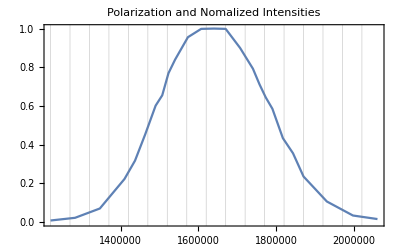

```mathematica
figure1=Transpose[{position,normalizedi}];
myrange=Range[1220000,2060000,50000];
ListLinePlot[figure1,Frame->True,GridLines->{myrange,myrange},PlotLabel->Style["Polarization and Nomalized Intensities"]]
```

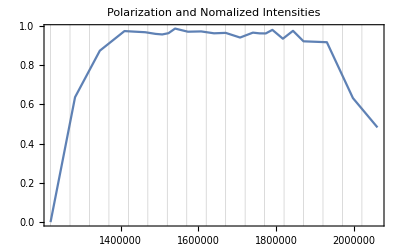

```mathematica
figure2=Transpose[{position,Polarization}];
ListLinePlot[figure2,Frame->True,GridLines->{myrange,myrange},PlotLabel->Style["Polarization and Nomalized Intensities"]]
```

```mathematica
deltaP=Map[ErrorBar,δP];
p=Transpose[{figure2,deltaP}];
deltai=Map[ErrorBar,δnormalizedi];
intensities=Transpose[{figure1,deltai}];
```

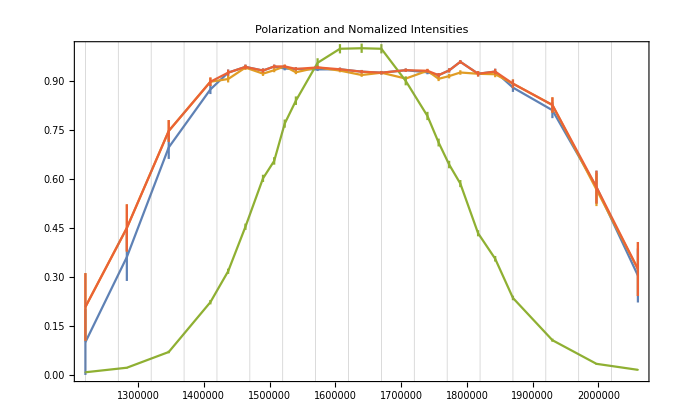

```mathematica
Needs["ErrorBarPlots`"]
ErrorListPlot[{plotcontrastA,plotcontrastB,intensities,plotcontrast},Frame->True,GridLines->{myrange,myrange},PlotLabel->Style["Polarization and Nomalized Intensities"],Joined->True,PlotLegends->"Expressions"]
```

```mathematica
e1 [Ioff,Iab,Ia,Ib]
Length[e1 [Ioff,Iab,Ia,Ib]];
Δe1[Ioff,Iab,Ia,Ib,ΔIoff,ΔIa,ΔIa,ΔIb]
e2 [Ioff,Iab,Ia,Ib] 
Δe2 [Ioff,Iab,Ia,Ib,ΔIoff,ΔIab,ΔIa,ΔIb]
```

{-7.84211,1.15106,0.974739,0.943387,0.959197,1.00389,1.0013,1.01799,1.01808,0.949843,0.999154,0.985194,0.990707,0.99388,1.02225,0.997917,0.977901,0.98828,0.962595,1.05237,0.9666,1.04786,0.980978,1.32088,1.31274}

{30.8281,0.299514,0.0782672,0.0333733,0.0267909,0.0227586,0.0200387,0.0192294,0.0178011,0.0160426,0.0157305,0.0152178,0.0154528,0.0155367,0.0167884,0.0174555,0.0183605,0.0191492,0.0190107,0.0250772,0.0253015,0.0356724,0.0546071,0.197972,0.540051}

{1.54902,0.838182,0.896278,0.916208,0.981124,1.00619,1.01196,1.03103,1.01059,0.961043,0.992574,0.989714,1.00219,0.993932,1.05291,0.992581,0.990649,1.0079,0.997986,1.0525,0.975612,1.0325,0.959749,1.34667,1.17818}

{2.6397,0.238536,0.0894234,0.0436645,0.0376863,0.031347,0.0277027,0.0266987,0.0241435,0.0224935,0.0214196,0.0210205,0.0213977,0.02122,0.023572,0.023704,0.0253947,0.0267981,0.0275349,0.0337653,0.0351273,0.0464624,0.0694389,0.230969,0.506854}

```mathematica
position
```

{1220000,1283000,1346700,1410000,1437000,1463300,1490000,1507000,1523000,1540000,1573000,1607000,1640000,1670000,1707000,1740000,1757000,1773000,1790000,1817000,1843000,1870000,1930000,1997000,2060000}

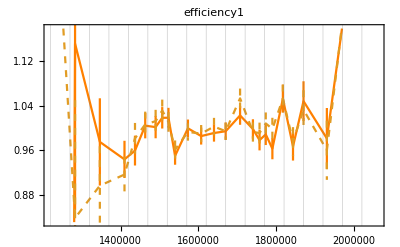

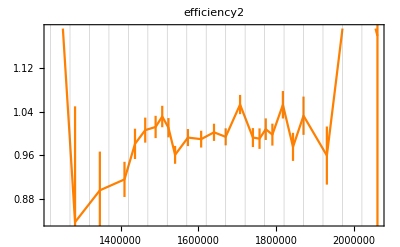

```mathematica
eff1=Transpose[{position,e1 [Ioff,Iab,Ia,Ib]}];
deltae1=Map[ErrorBar,Δe1[Ioff,Iab,Ia,Ib,ΔIoff,ΔIa,ΔIa,ΔIb]];
eff2=Transpose[{position,e2 [Ioff,Iab,Ia,Ib]}];
deltae2=Map[ErrorBar,Δe2[Ioff,Iab,Ia,Ib,ΔIoff,ΔIa,ΔIa,ΔIb]];

ef1plot=Transpose[{eff1,deltae1}];
ef2plot=Transpose[{eff2,deltae2}];
ErrorListPlot[{ef1plot,ef2plot},Frame->True,GridLines->{myrange,myrange},PlotLabel->Style["efficiency1"],Joined->True,PlotStyle->{Orange,Dashed}]
ErrorListPlot[{ef2plot},Frame->True,GridLines->{myrange,myrange},PlotLabel->Style["efficiency2"],Joined->True,PlotStyle->Orange]
```

```mathematica
Intensities=Partition[Data2,4];
```

```mathematica
Imax=Map[Max,Intensities];
Imin=Map[Min,Intensities];
ΔImax=Map[Sqrt,Imax];
ΔImin=Map[Sqrt,Imin];
```

```mathematica
Imax;
Imina=Ia;
ΔImina=Map[Sqrt,Imina];
Iminb=Ib;
ΔIminb=Map[Sqrt,Iminb];
```

```mathematica
Contrast[Imax,Imina];
ErrContrast[Imax,Imina,ΔImax,ΔImina];
Contrast[Imax,Iminb];
ErrContrast[Imax,Iminb,ΔImax,ΔIminb];
```

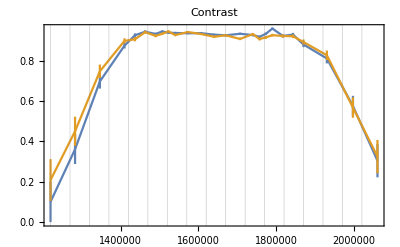

```mathematica
contrastA=Transpose[{position,Contrast[Imax,Imina]}];
deltacontrastA=Map[ErrorBar,ErrContrast[Imax,Imina,ΔImax,ΔImina]];
plotcontrastA=Transpose[{contrastA,deltacontrastA}];

contrastB=Transpose[{position,Contrast[Imax,Iminb]}];
deltacontrastB=Map[ErrorBar,ErrContrast[Imax,Iminb,ΔImax,ΔIminb]];
plotcontrastB=Transpose[{contrastB,deltacontrastB}];

ErrorListPlot[{plotcontrastA,plotcontrastB},Frame->True,GridLines->{myrange,myrange},PlotLabel->Style["Contrast"],Joined->True]
```